# Thermalisation Times

Simple Bertoni level approx to non-relativistic approx to therm time for different interactions. Can just swap out the squared matrix elements to find the squared coupling as a function of mass. Need to do the cross sections separately though.

```mathematica
Clear["Global`*"]
ClearSystemCache[]
SetDirectory[NotebookDirectory[]];
```

## Global Constants

```mathematica
TEMP = ((1*^3*1*^-9)/(1.16*^4)); (* GeV *)
NM     = (0.939); (* GeV *)
SOL   = 299792458.; (* ms^-1 *)
VELDISP  = 270.*^3;(* ms^-1 *)
NSVEL =  200.*^3 ;(* ms^-1 *)
G       =  6.67408*^-11; (*Grav Constant*)
TT = ((1*^10 * 3.154*^7)/(6.58*^-16)*1*^9); (* therm time *)
```

## Matrix Elements

```mathematica
(*================================================================================================================================================================*)

(* S = scalar, Ps = Psedoscalar, V = vector, Av = Axialovector *)

SSME[q_, dmm_] := 16*NM^2*dmm^2; (* same as vector-vector *)

PsSME[q_, dmm_] := 4*NM^2*q^2;

SPsME[q_, dmm_] := 4*dmm^2*q^2;

PsPsME[q_, dmm_] := q^4;

AvAvME[q_, dmm_] := 12*NM^2*dmm^2;

TTME[q_, dmm_] :=  3*NM^2*dmm^2;
```

## Actual Stuff

```mathematica
responseFn[q_, q0_] := (NM^2*q0)/(Pi*q);
denomInt[ki_, ME_, dmm_] :=Module[
{q, q0, cos},
q = √(ki^2+kp^2- 2* ki*kp*cos);
q0 = 1/(2*dmm)*(ki^2- kp^2);
 Integrate[(ME[q, dmm]*q0)/(16*NM^2*dmm^2*(2*π)^2)*kp^2*responseFn[q, q0],{kp, 0, ki}, {cos, -1, 1}, Assumptions->{ki>kp, kp>0}]
];

gSqr[ME_, dmm_] := Module[(*coupling constant squared in Natural units*)
{k0, kn},
k0 = dmm/3;
kn = √(4*dmm*TEMP);
-1/TT*Integrate[ki/(dmm*denomInt[ki, ME, dmm]), {ki, k0, kn}, Assumptions->{k0>kn, kn>0}]
];
```

## Cross Sections

```mathematica
ssCS[dmm_] := gSqr[ssME, dmm]/2* (NM^2*dmm^2)/(NM + dmm)^2*(1/(1.97*^7)*1*^-9)^2*1*^4;
```

## Plots

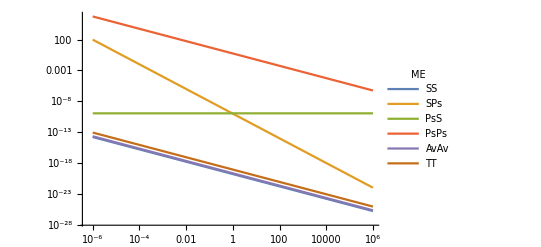

```mathematica
ListLogLogPlot[ Evaluate@Table[
With[
{x:=10^xp}, 
Table[
{x, gSqr[ME,x]},
 {xp, -6, 6, 0.5}
]
], {ME,{SSME,SPsME, PsSME, PsPsME, AvAvME, TTME}}
], 
PlotLegends->LineLegend[
Table[ME,{ME,{"SS", "SPs", "PsS", "PsPs", "AvAv", "TT"}} ],
LegendLabel->"ME"
],
Joined->True
]
```